# Trabalho Computacional II

## Análise Numérica [2016/2017]

Sara Cruz 		#79410
Fernando Subtil	#81085
Matilde Farinha	#81240

## 1.

#### Método de Runge - Kutta

A partir da tabela de Butcher, temos os coeficientes do método de Runge-Kutta a 3 etapas.

```mathematica
A={{0,0,0},{1/4,1/4,0},{0,1,0}};
c={0,1/2,1};
b={1/6,2/3,1/6};
<<NumericalDifferentialEquationAnalysis`;
Grid[Prepend[Table[
(* ordem *)
{p,
(* verifica se todas as condições são satisfeitas *)
Apply[And,Map[Function[l,Apply[And,l]],
(* lista as condições de ordem p de um método de Runge Kutta de 3 etapas *)
RungeKuttaOrderConditions[p,3]
(* substitui os coeficientes das condições pelos dados na tabela de Butcher *)
/.{Subscript[a, 1,1]->A[[1,1]],Subscript[a, 1,2]->A[[1,2]],Subscript[a, 1,3]->A[[1,3]], Subscript[a, 2,1]->A[[2,1]],Subscript[a, 2,2]->A[[2,2]],Subscript[a, 2,3]->A[[2,3]], Subscript[a, 3,1]->A[[3,1]],Subscript[a, 3,2]->A[[3,2]],Subscript[a, 3,3]->A[[3,3]],Subscript[b, 1]->b[[1]],Subscript[b, 2]->b[[2]],Subscript[b, 3]->b[[3]],Subscript[c, 1]->c[[1]],Subscript[c, 2]->c[[2]],Subscript[c, 3]->c[[3]]}]]},
{p,1,6}], {"Ordem", "Satisfaz condições"}],Frame->All]
```

Ordem | Satisfaz condições
1 | True
2 | True
3 | True
4 | True
5 | False
6 | False

```mathematica
(* polinómio de estabilidade do método IRK *)
pEstRK=Det[IdentityMatrix[3]-h*A+h*Outer[Times,{1,1,1},b]]/Det[IdentityMatrix[3]-h*A]
```

(432+324 h+108 h^2+18 h^3)/(108 (4-h))

```mathematica
(* região de estabilidade *)
regRK=Reduce[Abs[pEstRK]<1,h,Complexes];
```

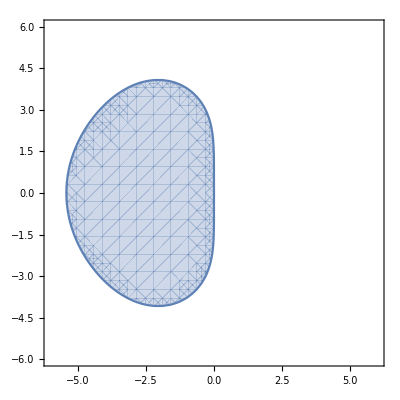

```mathematica
RegionPlot[regRK
/.h->(x+y*I),{x,-6,6},{y,-6,6}, Axes->True]
```

#### Método de Milne - Simpson

```mathematica
Clear[h,z];
(* primeiro polinómio característico do métdo de Milne-Simpson *)
rMS=z^2-1;
(* segundo polinómio característico *) 
sMS=z^2/3+4/3*z+1/3;
(* polinómio de estabilidade *)
pEstMS=rMS-h*sMS;
(* raízes do polinómio de estabilidade *)
{r1,r2}=Solve[pEstMS==0,z,Complexes]
```

{{z→(-2 h-√3 √(3+h^2))/(-3+h)},{z→(-2 h+√3 √(3+h^2))/(-3+h)}}

```mathematica
sol=Solve[pEstMS==0,h,Complexes][[1]]
```

{h→(3 (-1+z^2))/(1+4 z+z^2)}

```mathematica
(* fronteira da região de estabilidade absoluta *)
frontEstMS=h/.sol/.z->(E^(I*t))
```

(3 (-1+ⅇ^(2 ⅈ t)))/(1+4 ⅇ^(ⅈ t)+ⅇ^(2 ⅈ t))

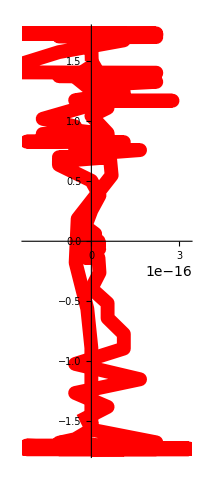

```mathematica
ParametricPlot[{Re[frontEstMS],Im[frontEstMS]},{t,0,2Pi},Axes->True,PlotStyle->Directive[Red,AbsoluteThickness[10]]]
```

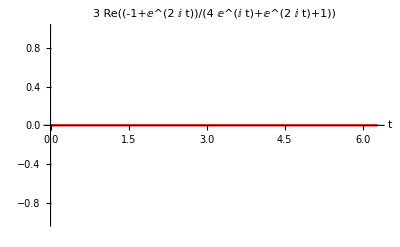

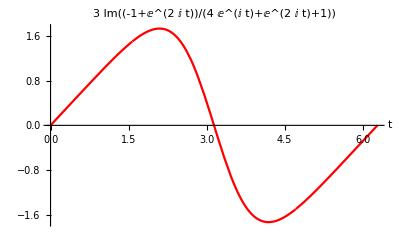

```mathematica
Plot[Chop[Re[frontEstMS]],{t,0,2Pi},AxesLabel->Automatic,PlotLabel->Re[frontEstMS], PlotStyle->Red]
Plot[Im[frontEstMS],{t,0,2Pi},AxesLabel->Automatic,PlotLabel->Im[frontEstMS], PlotStyle->Red]
```

```mathematica
Grid[Prepend[Table[{t,Chop[N[Re[frontEstMS]]],N[Im[frontEstMS]]},{t,0,2Pi,Pi/4}],{"t","Re[frontEstMS]","Im[frontEstMS]"}],Frame->All]
```

t | Re[frontEstMS] | Im[frontEstMS]
0 | 0 | 0.
π/4 | 0 | 0.783612
π/2 | 0 | 1.5
(3 π)/4 | 0 | 1.64075
π | 0 | 0.
(5 π)/4 | 0 | -1.64075
(3 π)/2 | 0 | -1.5
(7 π)/4 | 0 | -0.783612
2 π | 0 | 0.

```mathematica
FindMinimum[Im[frontEstMS],{t,3/4*Pi}]
```

{-1.73205,{t→4.18879}}

```mathematica
FindMaximum[Im[frontEstMS],t]
```

{1.73205,{t→2.0944}}

#### Método de Adams - Moulton

Cálculo dos b_j’s para o método de Adams - Moulton de ordem 4

```mathematica
aAM={0,0,-1,1};
bAM=Table[Integrate[Product[(s-i)/(j-i),{i,Select[Table[k,{k,0,3}],#≠j&]}],{s,2,3}],{j,0,3}]
```

{1/24,-5/24,19/24,3/8}

Satisfação das condições de ordem de consistência

```mathematica
Grid[Prepend[Prepend[Table[{k,Sum[j^k*aAM[[j+1]],{j,0,3}]==k*Sum[j^(k-1)*bAM[[j+1]],{j,0,3}]},{k,2,4}],{1,Sum[j*aAM[[j+1]],{j,0,3}]==Sum[bAM[[j+1]],{j,0,3}]}],{"Ordem","Satisfaz"}],Frame->All]
```

Ordem | Satisfaz
1 | True
2 | True
3 | True
4 | True

Construção dos polinómios

```mathematica
Clear[z,h];
(* primeiro polinómio característico do método de Adams-Moulton *)
rAM=z^2*(z-1);
(* segundo polinómio característico *) 
sAM=0;For[i=1,i≤Length[bAM],i++,sAM=sAM+z^(i-1)*bAM[[i]]]
(* polinómio de estabilidade *)
pEstAM=rAM-h*sAM;
(* raízes do polinómio de estabilidade *)
{z1,z2,z3}=Solve[pEstAM==0,z,Complexes];
(* fronteira da região de estabilidade absoluta *)
regAM=h/.Solve[pEstAM==0,h,Complexes][[1]]
```

(24 (-1+z) z^2)/(1-5 z+19 z^2+9 z^3)

```mathematica
ParametricPlot[{Re[regAM/.z->(E^(I*t))],Im[regAM/.z->(E^(I*t))]},{t,0,2Pi},PlotRange->{{-6,6},{-6,6}}]/.l_Line:>{EdgeForm[Directive[AbsoluteThickness[1],RGBColor[0.41,0.51,0.72]]],RGBColor[0.41,0.51,0.72],FilledCurve[l]}
```

-Graphics-

Escolhendo um ponto do interior da região delimitada pela fronteira de estabilidade absoluta, verifica-se que todas as raízes que satisfazem a condição da raiz para um valor fixo de h.

```mathematica
Grid[{{1,(Abs[z]/.z1/.h->-1)<1},{2,(Abs[z]/.z2/.h->-1)<1},{3,(Abs[z]/.z3/.h->-1)<1}},Frame->All]
```

1 | True
2 | True
3 | True

## 2.

### a)

Matriz associada ao problema é

```mathematica
Clear[A];
MatrixForm[A={{0,1},{-199,-200}}]
```

(0 | 1
-199 | -200)

No nosso caso a matriz A do problema dado não depende do tempo, contudo tem-se em geral que esta pode depender do tempo. Definimos por isso

```mathematica
H[t_]:={{0,1},{-199,-200}};
```

### b)

Valores próprios de A

```mathematica
{l1,l2}=Eigenvalues[A]
```

{-199,-1}

Vectores próprios associados aos valores próprios de A

```mathematica
{u1,u2}=Eigenvectors[A]
```

{{-1,199},{-1,1}}

### c)

Cálculo dos coeficientes c1 e c2 a partir das condições iniciais do problema

```mathematica
sol=Solve[c1*u1+c2*u2=={1,197} ,{c1,c2}][[1]]
```

{c1→1,c2→-2}

Solução exacta

```mathematica
X[t_]:=c1*E^(l1*t)*u1+c2*E^(l2*t)*u2/.sol
X[t]
```

{-ⅇ^(-199 t)+2 ⅇ^-t,199 ⅇ^(-199 t)-2 ⅇ^-t}

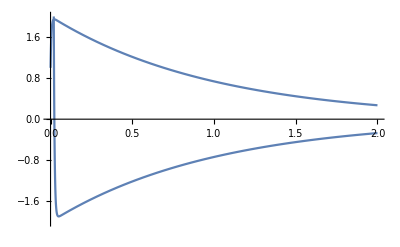

```mathematica
pEx1=Plot[X[t][[1]],{t,0,2},PlotRange->{{0,2},{-2,2}},PlotLegends-> "Y"];
pEx2=Plot[X[t][[2]],{t,0,2},PlotRange->{{0,2},{-2,2}},PlotLegends-> "Y'"];
Show[pEx1,pEx2]
```

### d)

#### Implementação dos métodos

Seguidamente encontram-se as funções definidas para a obtenção das aproximações pelos métodos de Runge-Kutta (RK), Runge-Kutta-Merson (RKM) e BDF de ordem 5 (BDF).

```mathematica
(* funções auxiliares para o cálculo dos coeficientes do método BDF *)
l=Function[{j,k},Product[(p-i)/(j-i),{i,Select[Table[l,{l,0,k}],#≠j&]}]];
(* função que devolve a lista dos coeficientes *)
coefBDF=Function[k,Module[{cf,r,c},
cf={-1};
For[i=0,i≤k,i++,
PrependTo[cf,D[l[i,k],p]/.p->0]];
c=cf[[k+1]];
cf=Map[Function[m,m/c],cf]
]];

RK=Function[{A,b,c,s,An,Y,h,T},
Module[{i,r,k,phi},
k={};
i=1;
r={Y};
While[i≤ T/h,
k={};
k=Append[k,N[An[h*i+c[[1]]*h].r[[i]]]];
k=Append[k,N[Inverse[IdentityMatrix[2]-A[[2,2]]*h*An[h*i+c[[2]]*h]].An[h*i+c[[2]]*h].(r[[i]]+h*A[[2,1]]*k[[1]])]];
k=Append[k,N[An[h*i+c[[3]]*h].(r[[i]]+h*k[[2]])]];
phi=∑_(j=1)^s b[[j]]*k[[j]];
r=Append[r,r[[i]]+h*phi];
i=i+1];
Map[Function[x,Chop[N[x,10]]],r]]];
RKM=Function[{A,b,c,s,An,Y,h,T},
Module[{i,r,k,phi,w},
k={};
i=1;
r={Y};
While[i≤ T/h,
k={};
k=Append[k,N[An[h*i+c[[1]]*h].r[[i]]]];
w=2;
While[w≤ s,
k=Append[k,N[An[h*i+c[[w]]*h].(r[[i]]+h*Sum[A[[w,j]]*k[[j]],{j,1,w-1}])]];
w=w+1;
];
phi=Sum[b[[j]]*k[[j]],{j,1,s}];
r=Append[r,r[[i]]+h*phi];
i=i+1];
Map[Function[x,Chop[N[x,10]]],r]]];
BDF=Function[{p,An,Y,h,T},
Module[{i,j,pol,F,M1,M2,r,yn,coef},
coef=coefBDF[p];
r={};
For[i=0,i<p,i++,
r=Append[r,X[i*h]]];
i=p;
While[i≤T/h ,
yn=Last[r];
pol=0;
For[j=p,j≥1,j--,
pol=pol+coef[[j]]*r[[i-p+j]]];
F=FindRoot[{x1,x2}+pol-coef[[p+2]]*h*An[i*h].{x1,x2},{{x1,First[yn]},{x2,Last[yn]}},Method->"Newton"];
yn={x1,x2}/.F;
r=Append[r,yn];
i++];
Map[Function[x,Chop[N[x,10]]],r]]];

(* coeficientes do método de Runge-Kutta dado pela tabela de Butcher do primeiro exercício *)
Ark={{0,0,0},{1/4,1/4,0},{0,1,0}};
brk={1/6,2/3,1/6};
crk={0,1/2,1};

(* coeficientes do método de Runge-Kutta-Merson *)
Arkm={{0,0,0,0,0},{1/3,0,0,0,0},{1/6,1/6,0,0,0}, {1/8,0,3/8,0,0},{1/2,0,-3/2,2,0}};
brkm={1/6,0,0,2/3,1/6};
crkm={0,1/3,1/3,1/2,1};

(* coeficientes do método BDF {Subscript[a, 0],Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[a, 5],Subscript[b, 5]} *)
cBDF=coefBDF[5]
```

{-12/137,75/137,-200/137,300/137,-300/137,1,60/137}

#### Determinação de valores de h apropriados

Valores reais de h que limitam a região de estabilidade absoluta para o método de RK:

```mathematica
(* Runge-Kutta *)
```

```mathematica
N[Solve[Abs[pEstRK]==1&&Im[h]==0,h]]
```

{{h→0.},{h→-5.41995}}

```mathematica
-5.419951893353394/-199
```

0.0272359

Construção do polinómio e região de estabilidade do método de Runge - Kutta - Merson

```mathematica
(* Runge-Kutta-Merson *)
```

```mathematica
Clear[h];
(* polinómio de estabilidade do método RKM *)
pEstRKM=Det[IdentityMatrix[5]-h*Arkm+h*Outer[Times,{1,1,1,1,1},brkm]]
```

(31104+31104 h+15552 h^2+5184 h^3+1296 h^4+216 h^5)/31104

```mathematica
(* região de estabilidade *)
regRKM=Reduce[Abs[pEstRKM]<1,h,Complexes];
```

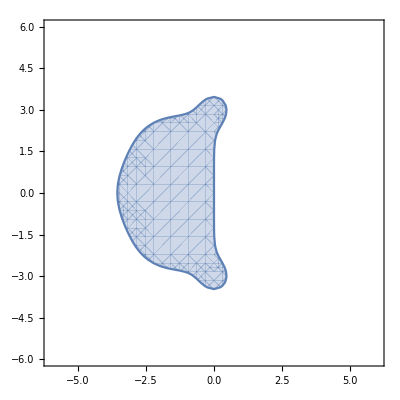

```mathematica
RegionPlot[regRKM/.h->(x+y*I),{x,-6,6},{y,-6,6}, Axes->True]
```

Valores reais de h que limitam a região de estabilidade absoluta para o método de RKM:

```mathematica
N[Solve[Abs[pEstRKM]==1&&Im[h]==0,h]]
```

{{h→0.},{h→-3.54832}}

```mathematica
-3.548322344234674/-199
```

0.0178308

Para o cálculo da região de estabilidade do método BDF de ordem 5, tem-se

```mathematica
(* BDF *)
```

```mathematica
Clear[z,h];
(* primeiro polinómio característico do método de BDF ordem 5 *)
rBDF=0;For[i=1,i≤(Length[cBDF]-1),i++,rBDF=rBDF+z^(i-1)*cBDF[[i]]]
(* segundo polinómio característico *) 
sBDF=Last[cBDF]*z^5;
(* polinómio de estabilidade *)
pEstBDF=rBDF-h*sBDF;
(* raízes do polinómio de estabilidade *)
{s1,s2,s3,s4,s5}=Solve[pEstBDF==0,z,Complexes];
(* fronteira da região de estabilidade absoluta *)
regBDF=h/.Solve[pEstBDF==0,h,Complexes][[1]]/.(z->(E^(I*t)))
```

1/60 ⅇ^(-5 ⅈ t) (-12+75 ⅇ^(ⅈ t)-200 ⅇ^(2 ⅈ t)+300 ⅇ^(3 ⅈ t)-300 ⅇ^(4 ⅈ t)+137 ⅇ^(5 ⅈ t))

```mathematica
ParametricPlot[{Re[regBDF],Im[regBDF]},{t,0,2Pi},Axes->True,Background->RGBColor[0.41,0.51,0.72,0.5]]/.
l_Line:>{EdgeForm[Directive[AbsoluteThickness[2],RGBColor[0.41,0.51,0.72]]],Opacity[1],White,FilledCurve[l]}
```

-Graphics-

Para h=5, tem-se

```mathematica
(Abs[z]/.s1/.h->5)<1
```

False

Pelo que a região de estabilidade será o lado exterior à fronteira desenhada.
De facto, escolhendo um ponto exterior, obtém-se

```mathematica
Grid[{{1,(Abs[z]/.s1/.h->-1)<1},{2,(Abs[z]/.s2/.h->-1)<1},{3,(Abs[z]/.s3/.h->-1)<1},{4,(Abs[z]/.s4/.h->-1)<1},{5,(Abs[z]/.s5/.h->-1)<1}},Frame->All]
```

1 | True
2 | True
3 | True
4 | True
5 | True

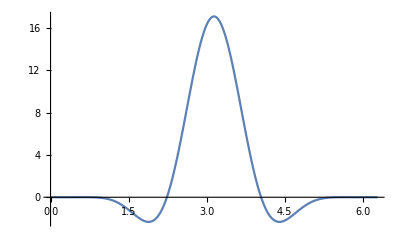

```mathematica
Plot[Re[regBDF],{t,0,2Pi}]
```

```mathematica
FindMaximum[Re[regBDF],{t,3/4Pi}]
```

{17.0667,{t→3.14159}}

#### Comparação de métodos

```mathematica
gEx1=Plot[X[t],{t,0,1},PlotRange->{-2,2},PlotStyle->Red,Ticks->{None,True}];
gEx2=Plot[X[t],{t,0,2},PlotRange->{-2,2},PlotStyle->Red,Ticks->{None,True}];
```

#### h = 0.01, T = 1

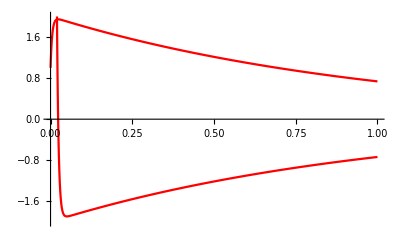
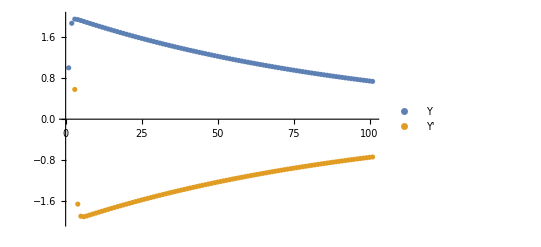

```mathematica
(* Runge-Kutta *)
rk011=RK[Ark,brk,crk,3,H,{1,197},0.01,1];
lrk011=Map[Function[x,First[x]],rk011];
lrk021=Map[Function[x,Last[x]],rk011];
grk011=ListPlot[{lrk011,lrk021},PlotRange->{-2,2},Ticks->{None,True},PlotLegends-> {"Y","Y'"}];
Overlay[{gEx1,grk011}]
```

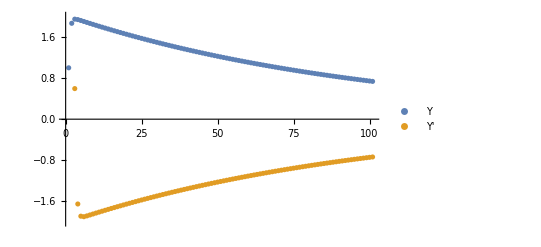
-Graphics--Graphics-

```mathematica
(* Runge-Kutta-Merson *)
rkm011=RKM[Arkm,brkm,crkm,5,H,{1,197},0.01,1];
lrkm011=Map[Function[x,First[x]],rkm011];
lrkm021=Map[Function[x,Last[x]],rkm011];
grkm011=ListPlot[{lrkm011,lrkm021},PlotRange->{-2,2},Ticks->{None,True},PlotLegends-> {"Y","Y'"}];
Overlay[{gEx1,grkm011}]
```

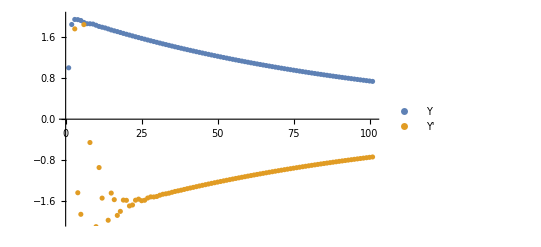
-Graphics--Graphics-

```mathematica
(* BDF *)
bdf011=BDF[5,H,{1,197},0.01,1];
lbdf011=Map[Function[x,First[x]],bdf011];
lbdf021=Map[Function[x,Last[x]],bdf011];
gbdf011=ListPlot[{lbdf011,lbdf021},PlotRange->{-2,2},Ticks->{None,True},PlotLegends-> {"Y","Y'"}];
Overlay[{gEx1,gbdf011}]
```

#### h=0.001, T=1

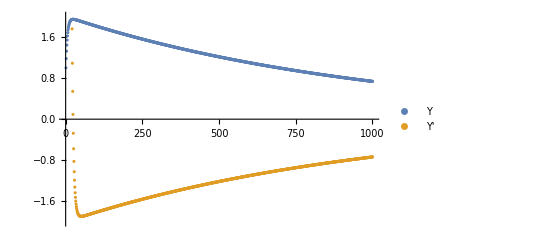
-Graphics--Graphics-

```mathematica
(* Runge-Kutta *)
rk0011=RK[Ark,brk,crk,3,H,{1,197},0.001,1];
lrk0011=Map[Function[x,First[x]],rk0011];
lrk0021=Map[Function[x,Last[x]],rk0011];
grk0011=ListPlot[{lrk0011,lrk0021},PlotRange->{-2,2},Ticks->{None,True},PlotLegends-> {"Y","Y'"}];
Overlay[{gEx1,grk0011}]
```

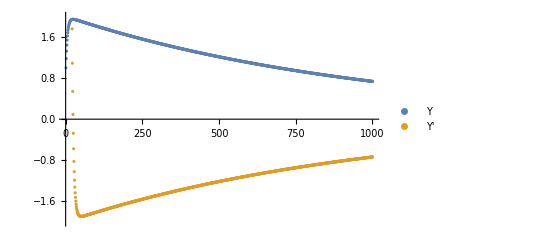
-Graphics--Graphics-

```mathematica
(* Runge-Kutta-Merson *)
rkm0011=RKM[Arkm,brkm,crkm,5,H,{1,197},0.001,1];
lrkm0011=Map[Function[x,First[x]],rkm0011];
lrkm0021=Map[Function[x,Last[x]],rkm0011];
grkm0011=ListPlot[{lrkm0011,lrkm0021},PlotRange->{-2,2},Ticks->{None,True},PlotLegends-> {"Y","Y'"}];
Overlay[{gEx1,grkm0011}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

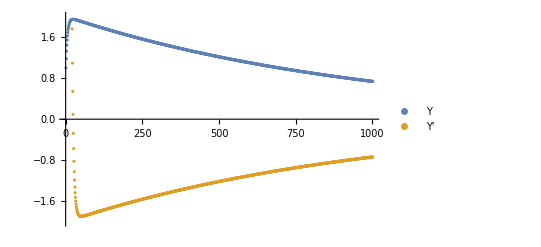
-Graphics--Graphics-

```mathematica
(* BDF *)
bdf0011=BDF[5,H,{1,197},0.001,1];
lbdf0011=Map[Function[x,First[x]],bdf0011];
lbdf0021=Map[Function[x,Last[x]],bdf0011];
gbdf0011=ListPlot[{lbdf0011,lbdf0021},PlotRange->{-2,2},Ticks->{None,True},PlotLegends-> {"Y","Y'"}];
Overlay[{gEx1,gbdf0011}]
```

#### h = 0.01, T = 2

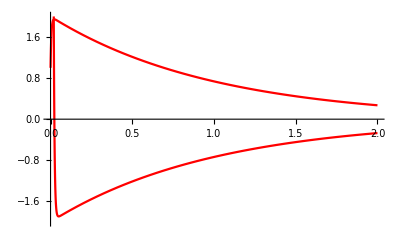
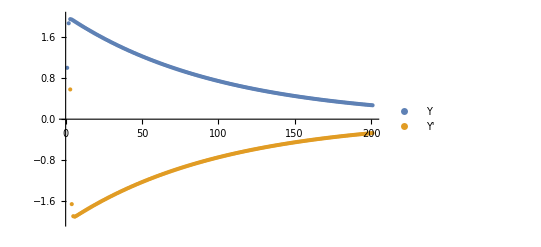

```mathematica
(* Runge-Kutta *)
rk012=RK[Ark,brk,crk,3,H,{1,197},0.01,2];
lrk012=Map[Function[x,First[x]],rk012];
lrk022=Map[Function[x,Last[x]],rk012];
grk012=ListPlot[{lrk012,lrk022},PlotRange->{-2,2},Ticks->{None,True},PlotLegends-> {"Y","Y'"}];
Overlay[{gEx2,grk012}]
```

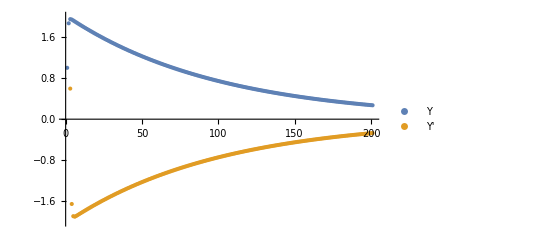
-Graphics--Graphics-

```mathematica
(* Runge-Kutta-Merson *)
rkm012=RKM[Arkm,brkm,crkm,5,H,{1,197},0.01,2];
lrkm012=Map[Function[x,First[x]],rkm012];
lrkm022=Map[Function[x,Last[x]],rkm012];
grkm012=ListPlot[{lrkm012,lrkm022},PlotRange->{-2,2},Ticks->{None,True},PlotLegends-> {"Y","Y'"}];
Overlay[{gEx2,grkm012}]
```

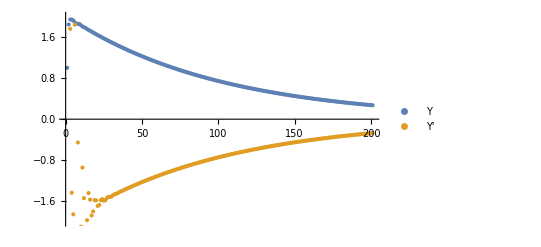
-Graphics--Graphics-

```mathematica
(* BDF *)
bdf012=BDF[5,H,{1,197},0.01,2];
lbdf012=Map[Function[x,First[x]],bdf012];
lbdf022=Map[Function[x,Last[x]],bdf012];
gbdf012=ListPlot[{lbdf012,lbdf022},PlotRange->{-2,2},Ticks->{None,True},PlotLegends-> {"Y","Y'"}];
Overlay[{gEx2,gbdf012}]
```

```mathematica
(* é preciso que os coeficientes dos métodos estejam atribuídos *)

tabelaaux=Function[{h,T,An,Y,E},
(*h: tamanho do passo 
T: instante final 
An: matriz do problema
Y: vector com valores iniciais
E: solução exacta *)

Module[{i,x,exact,diff1,diff2,diff3,l,r1,r2,r3,M1,M2,M3,max1,max2,max3},
i=1;
x={0};
exact={E[0]};
diff1={{Abs[Y[[1]]-exact[[1,1]]],Abs[Y[[2]]-exact[[1,2]]]}};
diff2={{Abs[Y[[1]]-exact[[1,1]]],Abs[Y[[2]]-exact[[1,2]]]}};
diff3={{Abs[Y[[1]]-exact[[1,1]]],Abs[Y[[2]]-exact[[1,2]]]}};
l={"x_n","Y_n","Y(x_n)","|Y(x_n)-Y_n|"};

(* aproximações *)
r1=RK[Ark,brk,crk,3,An,Y,h,T];(* Runge-Kutta *)
r2=RKM[Arkm,brkm,crkm,5,An,Y,h,T];(* Runge-Kutta-Merson *)
r3=BDF[5,An,Y,h,T]; (* BDF *)

(* cálculo do erro em cada Subscript[t, k] *)
While[i≤T/h, 
x=Append[x,i*h];
exact=Append[exact,E[i*h]]; 
diff1=Append[diff1,{Chop[Abs[r1[[i+1,1]]-exact[[i+1,1]]]],Chop[Abs[r1[[i+1,2]]-exact[[i+1,2]]]]}];
diff2=Append[diff2,{Chop[Abs[r2[[i+1,1]]-exact[[i+1,1]]]],Chop[Abs[r2[[i+1,2]]-exact[[i+1,2]]]]}];
diff3=Append[diff3,{Chop[Abs[r3[[i+1,1]]-exact[[i+1,1]]]],Chop[Abs[r3[[i+1,2]]-exact[[i+1,2]]]]}];
i=i+1];
i=1;
M1={l};
M2={l};
M3={l};
While[i≤Length[x],
M1=Append[M1,{x[[i]],r1[[i]],exact[[i]],diff1[[i]]}];
M2=Append[M2,{x[[i]],r2[[i]],exact[[i]],diff2[[i]]}];
M3=Append[M3,{x[[i]],r3[[i]],exact[[i]],diff3[[i]]}];
i=i+1];
{M1,M2,M3}
]];
```

```mathematica
tirazeros=Function[w,Table[Select[w[[i]],Function[l,l[[4]]≠{0,0}]],{i,1,3}]];
```

```mathematica
err011=tabelaaux[0.01,1,H,{1,197},X];
m011=tirazeros[err011];
err012=tabelaaux[0.01,2,H,{1,197},X];
m012=tirazeros[err012];
err0011=tabelaaux[0.001,1,H,{1,197},X];
m0011=tirazeros[err0011];
err0012=tabelaaux[0.001,2,H,{1,197},X];
m0012=tirazeros[err0012];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
Grid[Prepend[Table[{err011[[1,i,1]],err011[[1,i,4]],err011[[2,i,4]],err011[[3,i,4]]},{i,2,40}],{"x_n","Erro RK","Erro RKM", "Erro BDF"}],Frame->All]
```

x_n | Erro RK | Erro RKM | Erro BDF
0 | {0,0} | {0,0} | {0,0}
0.01 | {0.0237293,4.72214} | {0.0233675,4.65014} | {0,0}
0.02 | {0.0059243,1.17894} | {0.00584243,1.16264} | {0,0}
0.03 | {0.00111264,0.221416} | {0.00109875,0.218651} | {0,0}
0.04 | {0.000186301,0.037074} | {0.000184205,0.0366568} | {0,0}
0.05 | {0.0000293309,0.00583685} | {0.0000290344,0.00577785} | {0.0187645,3.73413}
0.06 | {4.44594×10^-6,0.000884743} | {4.40569×10^-6,0.000876732} | {0.0245203,4.87954}
0.07 | {6.57052×10^-7,0.000130754} | {6.51742×10^-7,0.000129696} | {0.00708524,1.40996}
0.08 | {9.53841×10^-8,0.0000189821} | {9.47021×10^-8,0.0000188453} | {0.00571505,1.1373}
0.09 | {1.36649×10^-8,2.71999×10^-6} | {1.35831×10^-8,2.70259×10^-6} | {0.00133261,0.265189}
0.1 | {1.9357×10^-9,3.85954×10^-7} | {1.931×10^-9,3.83772×10^-7} | {0.004361,0.86784}
0.11 | {2.69027×10^-10,5.43527×10^-8} | {2.74518×10^-10,5.40872×10^-8} | {0.00127908,0.254536}
0.12 | {0,7.60642×10^-9} | {0,7.58021×10^-9} | {0.00264214,0.525785}
0.13 | {0,1.05599×10^-9} | {0,1.05982×10^-9} | {0.00106395,0.211727}
0.14 | {0,1.42213×10^-10} | {0,1.50184×10^-10} | {0.00150626,0.299745}
0.15 | {0,0} | {0,0} | {0.000776274,0.154478}
0.16 | {0,0} | {0,0} | {0.00085131,0.169411}
0.17 | {0,0} | {0,0} | {0.000541862,0.10783}
0.18 | {0,0} | {0,0} | {0.000477195,0.0949618}
0.19 | {0,0} | {0,0} | {0.000371722,0.0739726}
0.2 | {0,0} | {0,0} | {0.000260728,0.051885}
0.21 | {0,0} | {0,0} | {0.000249111,0.0495731}
0.22 | {0,0} | {0,0} | {0.000138602,0.0275818}
0.23 | {0,0} | {0,0} | {0.000163867,0.0326095}
0.24 | {0,0} | {0,0} | {0.0000710899,0.0141469}
0.25 | {0,0} | {0,0} | {0.000106131,0.0211201}
0.26 | {0,0} | {0,0} | {0.0000346197,0.00688932}
0.27 | {0,0} | {0,0} | {0.0000677867,0.0134896}
0.28 | {0,0} | {0,0} | {0.0000155148,0.00308745}
0.29 | {0,0} | {0,0} | {0.0000427448,0.00850621}
0.3 | {0,0} | {0,0} | {5.92164×10^-6,0.00117841}
0.31 | {0,0} | {0,0} | {0.0000266318,0.00529973}
0.32 | {0,0} | {0,0} | {1.39961×10^-6,0.000278521}
0.33 | {0,0} | {0,0} | {0.0000164018,0.00326395}
0.34 | {0,0} | {0,0} | {5.12281×10^-7,0.000101943}
0.35 | {0,0} | {0,0} | {9.98672×10^-6,0.00198736}
0.36 | {0,0} | {0,0} | {1.14626×10^-6,0.000228107}
0.37 | {0,0} | {0,0} | {6.01115×10^-6,0.00119622}
0.38 | {0,0} | {0,0} | {1.20234×10^-6,0.000239264}

```mathematica
Grid[Prepend[Table[{err0011[[1,i,1]],err0011[[1,i,4]],err011[[2,i,4]],err011[[3,i,4]]},{i,2,40}],{"x_n","Erro RK","Erro RKM", "Erro BDF"}],Frame->All]
```

x_n | Erro RK | Erro RKM | Erro BDF
0 | {0,0} | {0,0} | {0,0}
0.001 | {5.79965×10^-7,0.000115413} | {0.0233675,4.65014} | {0,0}
0.002 | {9.5062×10^-7,0.000189173} | {0.00584243,1.16264} | {0,0}
0.003 | {1.16862×10^-6,0.000232555} | {0.00109875,0.218651} | {0,0}
0.004 | {1.27699×10^-6,0.000254121} | {0.000184205,0.0366568} | {0,0}
0.005 | {1.3082×10^-6,0.000260331} | {0.0000290344,0.00577785} | {0.0187645,3.73413}
0.006 | {1.28656×10^-6,0.000256025} | {4.40569×10^-6,0.000876732} | {0.0245203,4.87954}
0.007 | {1.23013×10^-6,0.000244796} | {6.51742×10^-7,0.000129696} | {0.00708524,1.40996}
0.008 | {1.15217×10^-6,0.000229283} | {9.47021×10^-8,0.0000188453} | {0.00571505,1.1373}
0.009 | {1.0623×10^-6,0.000211397} | {1.35831×10^-8,2.70259×10^-6} | {0.00133261,0.265189}
0.01 | {9.67339×10^-7,0.0001925} | {1.931×10^-9,3.83772×10^-7} | {0.004361,0.86784}
0.011 | {8.72061×10^-7,0.00017354} | {2.74518×10^-10,5.40872×10^-8} | {0.00127908,0.254536}
0.012 | {7.79669×10^-7,0.000155154} | {0,7.58021×10^-9} | {0.00264214,0.525785}
0.013 | {6.92226×10^-7,0.000137753} | {0,1.05982×10^-9} | {0.00106395,0.211727}
0.014 | {6.10953×10^-7,0.00012158} | {0,1.50184×10^-10} | {0.00150626,0.299745}
0.015 | {5.36471×10^-7,0.000106758} | {0,0} | {0.000776274,0.154478}
0.016 | {4.68976×10^-7,0.0000933261} | {0,0} | {0.00085131,0.169411}
0.017 | {4.08371×10^-7,0.0000812657} | {0,0} | {0.000541862,0.10783}
0.018 | {3.54367×10^-7,0.000070519} | {0,0} | {0.000477195,0.0949618}
0.019 | {3.06556×10^-7,0.0000610046} | {0,0} | {0.000371722,0.0739726}
0.02 | {2.64461×10^-7,0.0000526277} | {0,0} | {0.000260728,0.051885}
0.021 | {2.27576×10^-7,0.0000452875} | {0,0} | {0.000249111,0.0495731}
0.022 | {1.95391×10^-7,0.0000388828} | {0,0} | {0.000138602,0.0275818}
0.023 | {1.67411×10^-7,0.0000333148} | {0,0} | {0.000163867,0.0326095}
0.024 | {1.43167×10^-7,0.0000284903} | {0,0} | {0.0000710899,0.0141469}
0.025 | {1.22221×10^-7,0.0000243221} | {0,0} | {0.000106131,0.0211201}
0.026 | {1.04173×10^-7,0.0000207305} | {0,0} | {0.0000346197,0.00688932}
0.027 | {8.86588×10^-8,0.0000176431} | {0,0} | {0.0000677867,0.0134896}
0.028 | {7.53514×10^-8,0.0000149949} | {0,0} | {0.0000155148,0.00308745}
0.029 | {6.39597×10^-8,0.000012728} | {0,0} | {0.0000427448,0.00850621}
0.03 | {5.42257×10^-8,0.0000107909} | {0,0} | {5.92164×10^-6,0.00117841}
0.031 | {4.5922×10^-8,9.13847×10^-6} | {0,0} | {0.0000266318,0.00529973}
0.032 | {3.88494×10^-8,7.73103×10^-6} | {0,0} | {1.39961×10^-6,0.000278521}
0.033 | {3.2834×10^-8,6.53396×10^-6} | {0,0} | {0.0000164018,0.00326395}
0.034 | {2.77245×10^-8,5.51717×10^-6} | {0,0} | {5.12281×10^-7,0.000101943}
0.035 | {2.33899×10^-8,4.65458×10^-6} | {0,0} | {9.98672×10^-6,0.00198736}
0.036 | {1.97169×10^-8,3.92365×10^-6} | {0,0} | {1.14626×10^-6,0.000228107}
0.037 | {1.66078×10^-8,3.30495×10^-6} | {0,0} | {6.01115×10^-6,0.00119622}
0.038 | {1.39788×10^-8,2.78178×10^-6} | {0,0} | {1.20234×10^-6,0.000239264}

```mathematica
er1={err011,err0011};
mt1={m011,m0011};
er2={err012,err0012};
mt2={m012,m0012};
int={0.01,0.001};
```

```mathematica
Grid[Prepend[Table[{int[[i]],Length[mt1[[i,1]]]+1,er1[[i,1,Length[mt1[[i,1]]]+3,1]],Length[mt2[[i,1]]]+1,er2[[i,1,Length[mt2[[i,1]]]+3,1]],Length[mt1[[i,2]]]+1,er1[[i,2,Length[mt1[[i,2]]]+3,1]],Length[mt2[[i,2]]]+1,er2[[i,2,Length[mt2[[i,2]]]+3,1]],Length[mt1[[i,3]]]+6,er1[[i,3,Length[mt1[[i,3]]]+8,1]],Length[mt2[[i,3]]]+6,er2[[i,3,Length[mt2[[i,3]]]+8,1]]},{i,1,2}],{"h","RK: T=1","x_n", "RK: T=2","x_n", "RKM: T=1","x_n", "RKM: T=2","", "BDF: T=1","x_n", "BDF: T=2","x_n"}],Frame->All]
```

h | RK: T=1 | x_n | RK: T=2 | x_n | RKM: T=1 | x_n | RKM: T=2 |  | BDF: T=1 | x_n | BDF: T=2 | x_n
0.01 | 15 | 0.15 | 15 | 0.15 | 15 | 0.15 | 15 | 0.15 | 100 | 1. | 102 | 1.02
0.001 | 94 | 0.094 | 94 | 0.094 | 92 | 0.092 | 92 | 0.092 | 112 | 0.112 | 112 | 0.112

### e)

Função que constrói as tabelas das aproximações dos métodos nesta alínea definidos, juntamente com os valores exactos em cada ponto, o erro da aproximação em cada ponto e o erro máximo

```mathematica
tabela=Function[{h,T,An,Y,E},Module[{l,er1,er2,er3,e11,e21,e31,e12,e22,e32,diff1,diff2,diff3,max1,max2,max3}, 
{er1,er2,er3}=tabelaaux[h,T,An,Y,E];
l=Length[er1];
diff1=Table[er1[[i,4]],{i,2,l}];
diff2=Table[er2[[i,4]],{i,2,l}];
diff3=Table[er3[[i,4]],{i,2,l}];
e11={};
e21={};
e31={};
e12={};
e22={};
e32={};
i=1;
While[i≤ T/h +1,
e11=Append[e11,diff1[[i,1]]];
e21=Append[e21,diff2[[i,1]]];
e31=Append[e31,diff3[[i,1]]];
e12=Append[e12,diff1[[i,2]]];
e22=Append[e22,diff2[[i,2]]];
e32=Append[e32,diff3[[i,2]]];
i=i+1];
max1={Max[e11],Max[e12]};
max2={Max[e21],Max[e22]};
max3={Max[e31],Max[e32]};

(*{max1,max2,max3}]];*)  (* descomentar para a construção da tabela dos máximos e comentar tudo daqui para baixo *) 

Print["Erro máximo do método RK é" MatrixForm[max1]];
Print["Erro máximo do método RKM é" MatrixForm[max2]];
Print["Erro máximo do método BDF é" MatrixForm[max3]];
PrependTo[er1[[1]],"RK"];
PrependTo[er2[[1]],"RKM"];
PrependTo[er3[[1]],"BDF"];
Table[PrependTo[er1[[i]],i-2],{i,2,Length[er1]}];
Table[PrependTo[er2[[i]],i-2],{i,2,Length[er2]}];
Table[PrependTo[er3[[i]],i-2],{i,2,Length[er3]}];
(*construção das tabelas*)
Grid[er1,Frame->All]
Grid[er2,Frame->All]
Grid[er3,Frame->All]]];
```

```mathematica
tabela[0.001,1,H,{1,197},X]
```

```mathematica
tabela[0.0001,1,H,{1,197},X]
```

```mathematica
tabela[0.02,1,H,{1,197},X]
```

Erro máximo do método RK é (0.345386
68.7317)

Erro máximo do método RKM é (3.63542×10^15
7.23449×10^17)

Erro máximo do método BDF é (0.0283834
5.6483)

BDF | x_n | Y_n | Y(x_n) | |Y(x_n)-Y_n|
0 | 0 | {1.,197.} | {1,197} | {0,0}
1 | 0.02 | {1.94171,1.75804} | {1.94171,1.75804} | {0,0}
2 | 0.04 | {1.92123,-1.8521} | {1.92123,-1.8521} | {0,0}
3 | 0.06 | {1.88352,-1.88223} | {1.88352,-1.88223} | {0,0}
4 | 0.08 | {1.84623,-1.84621} | {1.84623,-1.84621} | {0,0}
5 | 0.1 | {1.78129,3.83862} | {1.80967,-1.80967} | {0.0283834,5.6483}
6 | 0.12 | {1.75065,2.84072} | {1.77384,-1.77384} | {0.0231888,4.61456}
7 | 0.14 | {1.74285,-2.56197} | {1.73872,-1.73872} | {0.00413697,0.823257}
8 | 0.16 | {1.711,-3.03923} | {1.70429,-1.70429} | {0.00670826,1.33494}
9 | 0.18 | {1.66592,-0.750413} | {1.67054,-1.67054} | {0.00462376,0.920128}
10 | 0.2 | {1.63434,-1.01597} | {1.63746,-1.63746} | {0.00312309,0.621495}
11 | 0.22 | {1.60824,-2.24224} | {1.60504,-1.60504} | {0.00320201,0.6372}
12 | 0.24 | {1.57464,-1.84825} | {1.57326,-1.57326} | {0.00138186,0.27499}
13 | 0.26 | {1.54013,-1.14845} | {1.5421,-1.5421} | {0.00197813,0.393649}
14 | 0.28 | {1.51106,-1.41157} | {1.51157,-1.51157} | {0.000502524,0.100002}
15 | 0.3 | {1.48281,-1.71539} | {1.48164,-1.48164} | {0.00117463,0.233752}
16 | 0.32 | {1.45241,-1.4747} | {1.4523,-1.4523} | {0.000112573,0.0224019}
17 | 0.34 | {1.42286,-1.28894} | {1.42354,-1.42354} | {0.000676371,0.134598}
18 | 0.36 | {1.39539,-1.40181} | {1.39535,-1.39535} | {0.0000324508,0.00645767}
19 | 0.38 | {1.3681,-1.44241} | {1.36772,-1.36772} | {0.000375288,0.0746824}
20 | 0.4 | {1.34057,-1.32646} | {1.34064,-1.34064} | {0.0000712351,0.0141758}
21 | 0.42 | {1.31389,-1.27417} | {1.31409,-1.31409} | {0.000200607,0.0399209}
22 | 0.44 | {1.28814,-1.30168} | {1.28807,-1.28807} | {0.0000683765,0.0136069}
23 | 0.46 | {1.26267,-1.28306} | {1.26257,-1.26257} | {0.000102956,0.0204882}
24 | 0.48 | {1.23751,-1.22703} | {1.23757,-1.23757} | {0.0000529574,0.0105386}
25 | 0.5 | {1.21301,-1.20305} | {1.21306,-1.21306} | {0.0000503139,0.0100125}
26 | 0.52 | {1.18908,-1.19637} | {1.18904,-1.18904} | {0.0000368515,0.0073334}
27 | 0.54 | {1.16552,-1.17008} | {1.1655,-1.1655} | {0.0000230363,0.00458417}
28 | 0.56 | {1.14239,-1.13765} | {1.14242,-1.14242} | {0.0000239489,0.0047659}
29 | 0.58 | {1.11979,-1.1179} | {1.1198,-1.1198} | {9.54532×10^-6,0.00189958}
30 | 0.6 | {1.09764,-1.10057} | {1.09762,-1.09762} | {0.0000147972,0.00294458}
31 | 0.62 | {1.07589,-1.07654} | {1.07589,-1.07589} | {3.26647×10^-6,0.000649965}
32 | 0.64 | {1.05458,-1.05284} | {1.05458,-1.05458} | {8.76955×10^-6,0.0017452}
33 | 0.66 | {1.0337,-1.03358} | {1.0337,-1.0337} | {5.9281×10^-7,0.000118034}
34 | 0.68 | {1.01324,-1.01423} | {1.01323,-1.01323} | {5.00815×10^-6,0.000996556}
35 | 0.7 | {0.99317,-0.993096} | {0.993171,-0.993171} | {3.75093×10^-7,0.0000747104}
36 | 0.72 | {0.973502,-0.972956} | {0.973505,-0.973505} | {2.75822×10^-6,0.000548954}
37 | 0.74 | {0.954228,-0.954347} | {0.954228,-0.954228} | {6.01385×10^-7,0.000119607}
38 | 0.76 | {0.935334,-0.935624} | {0.935333,-0.935333} | {1.46413×10^-6,0.000291294}
39 | 0.78 | {0.916811,-0.916704} | {0.916812,-0.916812} | {5.44187×10^-7,0.000108363}
40 | 0.8 | {0.898657,-0.89851} | {0.898658,-0.898658} | {7.44462×10^-7,0.000148218}
41 | 0.82 | {0.880864,-0.880945} | {0.880863,-0.880863} | {4.11462×10^-7,0.00008181}
42 | 0.84 | {0.863421,-0.863493} | {0.863421,-0.863421} | {3.60385×10^-7,0.0000716452}
43 | 0.86 | {0.846324,-0.846268} | {0.846324,-0.846324} | {2.81387×10^-7,0.0000560678}
44 | 0.88 | {0.829566,-0.829534} | {0.829566,-0.829566} | {1.61914×10^-7,0.0000322932}
45 | 0.9 | {0.81314,-0.813175} | {0.813139,-0.813139} | {1.81515×10^-7,0.0000360488}
46 | 0.92 | {0.797038,-0.797051} | {0.797038,-0.797038} | {6.58543×10^-8,0.0000130321}
47 | 0.94 | {0.781256,-0.781234} | {0.781256,-0.781256} | {1.10601×10^-7,0.0000220829}
48 | 0.96 | {0.765786,-0.765782} | {0.765786,-0.765786} | {2.06977×10^-8,4.19228×10^-6}
49 | 0.98 | {0.750622,-0.750635} | {0.750622,-0.750622} | {6.56579×10^-8,0.0000129923}
50 | 1. | {0.735759,-0.735759} | {0.735759,-0.735759} | {2.96591×10^-9,5.1641×10^-7} RK | x_n | Y_n | Y(x_n) | |Y(x_n)-Y_n|
0 | 0 | {1.,197.} | {1,197} | {0,0}
1 | 0.02 | {2.2871,-66.9737} | {1.94171,1.75804} | {0.345386,68.7317}
2 | 0.04 | {1.81485,19.3183} | {1.92123,-1.8521} | {0.106384,21.1704}
3 | 0.06 | {1.9184,-8.82258} | {1.88352,-1.88223} | {0.0348761,6.94035}
4 | 0.08 | {1.83484,0.420755} | {1.84623,-1.84621} | {0.0113918,2.26696}
5 | 0.1 | {1.8134,-2.5503} | {1.80967,-1.80967} | {0.00372173,0.740625}
6 | 0.12 | {1.77262,-1.53188} | {1.77384,-1.77384} | {0.00121589,0.241962}
7 | 0.14 | {1.73911,-1.81777} | {1.73872,-1.73872} | {0.000397231,0.079049}
8 | 0.16 | {1.70416,-1.67846} | {1.70429,-1.70429} | {0.000129775,0.0258253}
9 | 0.18 | {1.67058,-1.67898} | {1.67054,-1.67054} | {0.0000423975,0.00843712}
10 | 0.2 | {1.63745,-1.63471} | {1.63746,-1.63746} | {0.0000138514,0.00275641}
11 | 0.22 | {1.60504,-1.60594} | {1.60504,-1.60504} | {4.5251×10^-6,0.000900518}
12 | 0.24 | {1.57325,-1.57296} | {1.57326,-1.57326} | {1.47851×10^-6,0.000294199}
13 | 0.26 | {1.5421,-1.5422} | {1.5421,-1.5421} | {4.82854×10^-7,0.0000961147}
14 | 0.28 | {1.51157,-1.51154} | {1.51157,-1.51157} | {1.57935×10^-7,0.0000314008}
15 | 0.3 | {1.48164,-1.48165} | {1.48164,-1.48164} | {5.14014×10^-8,0.0000102585}
16 | 0.32 | {1.4523,-1.45229} | {1.4523,-1.4523} | {1.69979×10^-8,3.35164×10^-6}
17 | 0.34 | {1.42354,-1.42354} | {1.42354,-1.42354} | {5.33947×10^-9,1.09477×10^-6}
18 | 0.36 | {1.39535,-1.39535} | {1.39535,-1.39535} | {1.9664×10^-9,3.57882×10^-7}
19 | 0.38 | {1.36772,-1.36772} | {1.36772,-1.36772} | {4.12564×10^-10,1.1669×10^-7}
20 | 0.4 | {1.34064,-1.34064} | {1.34064,-1.34064} | {3.72109×10^-10,3.836×10^-8}
21 | 0.42 | {1.31409,-1.31409} | {1.31409,-1.31409} | {1.22836×10^-10,1.22878×10^-8}
22 | 0.44 | {1.28807,-1.28807} | {1.28807,-1.28807} | {2.10979×10^-10,4.26554×10^-9}
23 | 0.46 | {1.26257,-1.26257} | {1.26257,-1.26257} | {1.88527×10^-10,1.1361×10^-9}
24 | 0.48 | {1.23757,-1.23757} | {1.23757,-1.23757} | {2.01857×10^-10,6.34611×10^-10}
25 | 0.5 | {1.21306,-1.21306} | {1.21306,-1.21306} | {2.03158×10^-10,0}
26 | 0.52 | {1.18904,-1.18904} | {1.18904,-1.18904} | {2.08062×10^-10,2.54251×10^-10}
27 | 0.54 | {1.1655,-1.1655} | {1.1655,-1.1655} | {2.11472×10^-10,1.96382×10^-10}
28 | 0.56 | {1.14242,-1.14242} | {1.14242,-1.14242} | {2.15065×10^-10,2.19994×10^-10}
29 | 0.58 | {1.1198,-1.1198} | {1.1198,-1.1198} | {2.18302×10^-10,2.16691×10^-10}
30 | 0.6 | {1.09762,-1.09762} | {1.09762,-1.09762} | {2.21368×10^-10,2.21895×10^-10}
31 | 0.62 | {1.07589,-1.07589} | {1.07589,-1.07589} | {2.24214×10^-10,2.24042×10^-10}
32 | 0.64 | {1.05458,-1.05458} | {1.05458,-1.05458} | {2.26865×10^-10,2.26921×10^-10}
33 | 0.66 | {1.0337,-1.0337} | {1.0337,-1.0337} | {2.29322×10^-10,2.29303×10^-10}
34 | 0.68 | {1.01323,-1.01323} | {1.01323,-1.01323} | {2.31593×10^-10,2.31599×10^-10}
35 | 0.7 | {0.993171,-0.993171} | {0.993171,-0.993171} | {2.33683×10^-10,2.33681×10^-10}
36 | 0.72 | {0.973505,-0.973505} | {0.973505,-0.973505} | {2.35601×10^-10,2.35601×10^-10}
37 | 0.74 | {0.954228,-0.954228} | {0.954228,-0.954228} | {2.3735×10^-10,2.3735×10^-10}
38 | 0.76 | {0.935333,-0.935333} | {0.935333,-0.935333} | {2.38938×10^-10,2.38938×10^-10}
39 | 0.78 | {0.916812,-0.916812} | {0.916812,-0.916812} | {2.4037×10^-10,2.40371×10^-10}
40 | 0.8 | {0.898658,-0.898658} | {0.898658,-0.898658} | {2.41652×10^-10,2.41652×10^-10}
41 | 0.82 | {0.880863,-0.880863} | {0.880863,-0.880863} | {2.42789×10^-10,2.42789×10^-10}
42 | 0.84 | {0.863421,-0.863421} | {0.863421,-0.863421} | {2.43786×10^-10,2.43786×10^-10}
43 | 0.86 | {0.846324,-0.846324} | {0.846324,-0.846324} | {2.44648×10^-10,2.44648×10^-10}
44 | 0.88 | {0.829566,-0.829566} | {0.829566,-0.829566} | {2.4538×10^-10,2.4538×10^-10}
45 | 0.9 | {0.813139,-0.813139} | {0.813139,-0.813139} | {2.45988×10^-10,2.45988×10^-10}
46 | 0.92 | {0.797038,-0.797038} | {0.797038,-0.797038} | {2.46475×10^-10,2.46475×10^-10}
47 | 0.94 | {0.781256,-0.781256} | {0.781256,-0.781256} | {2.46847×10^-10,2.46846×10^-10}
48 | 0.96 | {0.765786,-0.765786} | {0.765786,-0.765786} | {2.47107×10^-10,2.47107×10^-10}
49 | 0.98 | {0.750622,-0.750622} | {0.750622,-0.750622} | {2.4726×10^-10,2.4726×10^-10}
50 | 1. | {0.735759,-0.735759} | {0.735759,-0.735759} | {2.4731×10^-10,2.4731×10^-10} RKM | x_n | Y_n | Y(x_n) | |Y(x_n)-Y_n|
0 | 0 | {1.,197.} | {1,197} | {0,0}
1 | 0.02 | {4.00784,-409.401} | {1.94171,1.75804} | {2.06613,411.159}
2 | 0.04 | {-2.27043,832.288} | {1.92123,-1.8521} | {4.19166,834.14}
3 | 0.06 | {10.4664,-1709.88} | {1.88352,-1.88223} | {8.58289,1708.}
4 | 0.08 | {-15.7267,3495.17} | {1.84623,-1.84621} | {17.5729,3497.01}
5 | 0.1 | {37.7892,-7161.74} | {1.80967,-1.80967} | {35.9795,7159.93}
6 | 0.12 | {-71.8921,14657.7} | {1.77384,-1.77384} | {73.6659,14659.5}
7 | 0.14 | {152.565,-30016.2} | {1.73872,-1.73872} | {150.826,30014.5}
8 | 0.16 | {-307.104,61451.1} | {1.70429,-1.70429} | {308.808,61452.8}
9 | 0.18 | {633.937,-125823.} | {1.67054,-1.67054} | {632.266,125821.}
10 | 0.2 | {-1292.89,257609.} | {1.63746,-1.63746} | {1294.53,257611.}
11 | 0.22 | {2652.07,-527444.} | {1.60504,-1.60504} | {2650.46,527442.}
12 | 0.24 | {-5425.09,1.07991×10^6} | {1.57326,-1.57326} | {5426.67,1.07991×10^6}
13 | 0.26 | {11112.3,-2.21105×10^6} | {1.5421,-1.5421} | {11110.8,2.21104×10^6}
14 | 0.28 | {-22747.1,4.52698×10^6} | {1.51157,-1.51157} | {22748.6,4.52698×10^6}
15 | 0.3 | {46577.9,-9.26872×10^6} | {1.48164,-1.48164} | {46576.5,9.26871×10^6}
16 | 0.32 | {-95361.,1.89771×10^7} | {1.4523,-1.4523} | {95362.5,1.89771×10^7}
17 | 0.34 | {195250.,-3.88545×10^7} | {1.42354,-1.42354} | {195249.,3.88545×10^7}
18 | 0.36 | {-399759.,7.95523×10^7} | {1.39535,-1.39535} | {399760.,7.95523×10^7}
19 | 0.38 | {818486.,-1.62879×10^8} | {1.36772,-1.36772} | {818485.,1.62879×10^8}
20 | 0.4 | {-1.6758×10^6,3.33484×10^8} | {1.34064,-1.34064} | {1.6758×10^6,3.33484×10^8}
21 | 0.42 | {3.4311×10^6,-6.82788×10^8} | {1.31409,-1.31409} | {3.4311×10^6,6.82788×10^8}
22 | 0.44 | {-7.02496×10^6,1.39797×10^9} | {1.28807,-1.28807} | {7.02496×10^6,1.39797×10^9}
23 | 0.46 | {1.43832×10^7,-2.86225×10^9} | {1.26257,-1.26257} | {1.43832×10^7,2.86225×10^9}
24 | 0.48 | {-2.94487×10^7,5.86029×10^9} | {1.23757,-1.23757} | {2.94487×10^7,5.86029×10^9}
25 | 0.5 | {6.02944×10^7,-1.19986×10^10} | {1.21306,-1.21306} | {6.02944×10^7,1.19986×10^10}
26 | 0.52 | {-1.23449×10^8,2.45664×10^10} | {1.18904,-1.18904} | {1.23449×10^8,2.45664×10^10}
27 | 0.54 | {2.52755×10^8,-5.02982×10^10} | {1.1655,-1.1655} | {2.52755×10^8,5.02982×10^10}
28 | 0.56 | {-5.175×10^8,1.02983×10^11} | {1.14242,-1.14242} | {5.175×10^8,1.02983×10^11}
29 | 0.58 | {1.05955×10^9,-2.10851×10^11} | {1.1198,-1.1198} | {1.05955×10^9,2.10851×10^11}
30 | 0.6 | {-2.16937×10^9,4.31704×10^11} | {1.09762,-1.09762} | {2.16937×10^9,4.31704×10^11}
31 | 0.62 | {4.44165×10^9,-8.83887×10^11} | {1.07589,-1.07589} | {4.44165×10^9,8.83887×10^11}
32 | 0.64 | {-9.094×10^9,1.80971×10^12} | {1.05458,-1.05458} | {9.094×10^9,1.80971×10^12}
33 | 0.66 | {1.86194×10^10,-3.70526×10^12} | {1.0337,-1.0337} | {1.86194×10^10,3.70526×10^12}
34 | 0.68 | {-3.81221×10^10,7.5863×10^12} | {1.01323,-1.01323} | {3.81221×10^10,7.5863×10^12}
35 | 0.7 | {7.80528×10^10,-1.55325×10^13} | {0.993171,-0.993171} | {7.80528×10^10,1.55325×10^13}
36 | 0.72 | {-1.59808×10^11,3.18019×10^13} | {0.973505,-0.973505} | {1.59808×10^11,3.18019×10^13}
37 | 0.74 | {3.27198×10^11,-6.51124×10^13} | {0.954228,-0.954228} | {3.27198×10^11,6.51124×10^13}
38 | 0.76 | {-6.69918×10^11,1.33314×10^14} | {0.935333,-0.935333} | {6.69918×10^11,1.33314×10^14}
39 | 0.78 | {1.37162×10^12,-2.72952×10^14} | {0.916812,-0.916812} | {1.37162×10^12,2.72952×10^14}
40 | 0.8 | {-2.8083×10^12,5.58852×10^14} | {0.898658,-0.898658} | {2.8083×10^12,5.58852×10^14}
41 | 0.82 | {5.74983×10^12,-1.14422×10^15} | {0.880863,-0.880863} | {5.74983×10^12,1.14422×10^15}
42 | 0.84 | {-1.17724×10^13,2.34271×10^15} | {0.863421,-0.863421} | {1.17724×10^13,2.34271×10^15}
43 | 0.86 | {2.41033×10^13,-4.79656×10^15} | {0.846324,-0.846324} | {2.41033×10^13,4.79656×10^15}
44 | 0.88 | {-4.93501×10^13,9.82067×10^15} | {0.829566,-0.829566} | {4.93501×10^13,9.82067×10^15}
45 | 0.9 | {1.01041×10^14,-2.01072×10^16} | {0.813139,-0.813139} | {1.01041×10^14,2.01072×10^16}
46 | 0.92 | {-2.06876×10^14,4.11683×10^16} | {0.797038,-0.797038} | {2.06876×10^14,4.11683×10^16}
47 | 0.94 | {4.23566×10^14,-8.42897×10^16} | {0.781256,-0.781256} | {4.23566×10^14,8.42897×10^16}
48 | 0.96 | {-8.67226×10^14,1.72578×10^17} | {0.765786,-0.765786} | {8.67226×10^14,1.72578×10^17}
49 | 0.98 | {1.77559×10^15,-3.53343×10^17} | {0.750622,-0.750622} | {1.77559×10^15,3.53343×10^17}
50 | 1. | {-3.63542×10^15,7.23449×10^17} | {0.735759,-0.735759} | {3.63542×10^15,7.23449×10^17}

```mathematica
tabela[0.01,1,H,{1,197},X]
```

```mathematica
tabela[0.005,1,H,{1,197},X]
```

```mathematica
tabela[0.0025,1,H,{1,197},X]
```

```mathematica
tabela[0.00125,1,H,{1,197},X]
```

```mathematica
tabela[0.000625,1,H,{1,197},X]
```

#### Valores máximos

```mathematica
h={0.02,0.01,0.005,0.0025,0.00125,0.001,0.000625};
(* calculado a partir de uma adaptação da função tabela sem prints nem Grid *)
erro1=Table[tabela[h[[i]],1,H,{1,197},X],{i,1,7}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Grid[Prepend[Table[{h[[i]],erro1[[i,1]],erro1[[i,2]],erro1[[i,3]]},{i,1,7}],{"h","erro max RK", "erro max RKM", "erro max BDF" }],Frame->All]
```

h | erro max RK | erro max RKM | erro max BDF
0.02 | {0.345386,68.7317} | {3.63542×10^15,7.23449×10^17} | {0.0283834,5.6483}
0.01 | {0.0237293,4.72214} | {0.0233675,4.65014} | {0.0245203,4.87954}
0.005 | {0.00118574,0.235961} | {0.000176911,0.0352054} | {0.00669291,1.33189}
0.0025 | {0.0000584018,0.011622} | {0.0000275799,0.00548839} | {0.000668968,0.133125}
0.00125 | {3.26402×10^-6,0.00064954} | {1.90618×10^-6,0.000379329} | {0.0000340875,0.00678341}
0.001 | {1.3082×10^-6,0.000260331} | {7.88533×10^-7,0.000156918} | {0.0000118733,0.00236278}
0.000625 | {1.9329×10^-7,0.0000384647} | {1.21538×10^-7,0.000024186} | {1.37074×10^-6,0.000272776}

### f) Análise dos erros

```mathematica
err021=tabelaaux[0.02,1,H,{1,197},X];
err011=tabelaaux[0.01,1,H,{1,197},X];
err0051=tabelaaux[0.005,1,H,{1,197},X];
err00251=tabelaaux[0.0025,1,H,{1,197},X];
err001251=tabelaaux[0.00125,1,H,{1,197},X];
err0006251=tabelaaux[0.000625,1,H,{1,197},X];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
err022=tabelaaux[0.02,2,H,{1,197},X];
err012=tabelaaux[0.01,2,H,{1,197},X];
err0052=tabelaaux[0.005,2,H,{1,197},X];
err00252=tabelaaux[0.0025,2,H,{1,197},X];
err001252=tabelaaux[0.00125,2,H,{1,197},X];
err0006252=tabelaaux[0.000625,2,H,{1,197},X];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
(* retiram-se os elementos cujo erro é 0, se a lista que resulta for igual à lista inicial, então não existem erros nulos *)
```

```mathematica
{m021,m011,m0051,m00251,m001251,m0006251}=Map[Function[w,Table[Select[w[[i]],Function[l,l[[4]]≠{0,0}]],{i,1,3}]],{err021,err011,err0051,err00251,err001251,err0006251}];
Map[Function[w,{Length[w[[1,1]]]==Length[w[[2,1]]]-2,Length[w[[1,2]]]==Length[w[[2,2]]]-2,Length[w[[1,3]]]==Length[w[[2,3]]]-6}],{{m021,err021},{m011,err011},{m0051,err0051},{m00251,err00251},{m001251,err001251},{m0006251,err0006251}}]
```

{{True,True,True},{False,False,False},{False,False,False},{False,False,False},{False,False,False},{False,False,False}}

```mathematica
{m022,m012,m0052,m00252,m001252,m0006252}=Map[Function[w,Table[Select[w[[i]],Function[l,l[[4]]≠{0,0}]],{i,1,3}]],{err022,err012,err0052,err00252,err001252,err0006252}];
Map[Function[w,{Length[w[[1,1]]]==Length[w[[2,1]]]-2,Length[w[[1,2]]]==Length[w[[2,2]]]-2,Length[w[[1,3]]]==Length[w[[2,3]]]-6}],{{m022,err022},{m012,err012},{m0052,err0052},{m00252,err00252},{m001252,err001252},{m0006252,err0006252}}]
```

{{True,True,True},{False,False,False},{False,False,False},{False,False,False},{False,False,False},{False,False,False}}

```mathematica
(* h=0.01 T=1 *)
{Length[err011[[1]]],Length[err011[[2]]],Length[err011[[3]]]}
{Length[m011[[1]]],Length[m011[[2]]],Length[m011[[3]]]}
```

{102,102,102}

{14,14,94}

```mathematica
Grid[Prepend[Join[Table[Prepend[err011[[1,i]],i-2],{i,2,14,2}],Table[Prepend[err011[[1,i]],i-2],{i,14,17}]],{"RK","x_n","Y_n","Y(x_n)","|Y(x_n)-Y_n|"}],Frame->All]
```

RK | x_n | Y_n | Y(x_n) | |Y(x_n)-Y_n|
0 | 0 | {1.,197.} | {1,197} | {0,0}
2 | 0.02 | {1.94764,0.579108} | {1.94171,1.75804} | {0.0059243,1.17894}
4 | 0.04 | {1.92142,-1.88917} | {1.92123,-1.8521} | {0.000186301,0.037074}
6 | 0.06 | {1.88353,-1.88312} | {1.88352,-1.88223} | {4.44594×10^-6,0.000884743}
8 | 0.08 | {1.84623,-1.84623} | {1.84623,-1.84621} | {9.53841×10^-8,0.0000189821}
10 | 0.1 | {1.80967,-1.80967} | {1.80967,-1.80967} | {1.9357×10^-9,3.85954×10^-7}
12 | 0.12 | {1.77384,-1.77384} | {1.77384,-1.77384} | {0,7.60642×10^-9}
12 | 0.12 | {1.77384,-1.77384} | {1.77384,-1.77384} | {0,7.60642×10^-9}
13 | 0.13 | {1.75619,-1.75619} | {1.75619,-1.75619} | {0,1.05599×10^-9}
14 | 0.14 | {1.73872,-1.73872} | {1.73872,-1.73872} | {0,1.42213×10^-10}
15 | 0.15 | {1.72142,-1.72142} | {1.72142,-1.72142} | {0,0}

```mathematica
Grid[Prepend[Join[Table[Prepend[err011[[2,i]],i-2],{i,2,14,2}],Table[Prepend[err011[[2,i]],i-2],{i,14,17}]],{"RKM","x_n","Y_n","Y(x_n)","|Y(x_n)-Y_n|"}],Frame->All]
```

RKM | x_n | Y_n | Y(x_n) | |Y(x_n)-Y_n|
0 | 0 | {1.,197.} | {1,197} | {0,0}
2 | 0.02 | {1.94755,0.595402} | {1.94171,1.75804} | {0.00584243,1.16264}
4 | 0.04 | {1.92141,-1.88875} | {1.92123,-1.8521} | {0.000184205,0.0366568}
6 | 0.06 | {1.88353,-1.88311} | {1.88352,-1.88223} | {4.40569×10^-6,0.000876732}
8 | 0.08 | {1.84623,-1.84623} | {1.84623,-1.84621} | {9.47021×10^-8,0.0000188453}
10 | 0.1 | {1.80967,-1.80967} | {1.80967,-1.80967} | {1.931×10^-9,3.83772×10^-7}
12 | 0.12 | {1.77384,-1.77384} | {1.77384,-1.77384} | {0,7.58021×10^-9}
12 | 0.12 | {1.77384,-1.77384} | {1.77384,-1.77384} | {0,7.58021×10^-9}
13 | 0.13 | {1.75619,-1.75619} | {1.75619,-1.75619} | {0,1.05982×10^-9}
14 | 0.14 | {1.73872,-1.73872} | {1.73872,-1.73872} | {0,1.50184×10^-10}
15 | 0.15 | {1.72142,-1.72142} | {1.72142,-1.72142} | {0,0}

```mathematica
Grid[Prepend[Join[Table[Prepend[err011[[3,i]],i-2],{i,2,91,10}],Table[Prepend[err011[[3,i]],i-2],{i,92,102}]],{"BDF","x_n","Y_n","Y(x_n)","|Y(x_n)-Y_n|"}],Frame->All]
```

BDF | x_n | Y_n | Y(x_n) | |Y(x_n)-Y_n|
0 | 0 | {1.,197.} | {1,197} | {0,0}
10 | 0.1 | {1.80531,-0.941835} | {1.80967,-1.80967} | {0.004361,0.86784}
20 | 0.2 | {1.63772,-1.68935} | {1.63746,-1.63746} | {0.000260728,0.051885}
30 | 0.3 | {1.48163,-1.48046} | {1.48164,-1.48164} | {5.92164×10^-6,0.00117841}
40 | 0.4 | {1.34064,-1.34043} | {1.34064,-1.34064} | {1.03344×10^-6,0.000205656}
50 | 0.5 | {1.21306,-1.2131} | {1.21306,-1.21306} | {1.95435×10^-7,0.0000388897}
60 | 0.6 | {1.09762,-1.09762} | {1.09762,-1.09762} | {2.12061×10^-8,4.22206×10^-6}
70 | 0.7 | {0.993171,-0.993171} | {0.993171,-0.993171} | {1.7061×10^-9,3.37321×10^-7}
80 | 0.8 | {0.898658,-0.898658} | {0.898658,-0.898658} | {0,1.87864×10^-8}
90 | 0.9 | {0.813139,-0.813139} | {0.813139,-0.813139} | {0,3.1375×10^-10}
91 | 0.91 | {0.805048,-0.805048} | {0.805048,-0.805048} | {0,2.09266×10^-9}
92 | 0.92 | {0.797038,-0.797038} | {0.797038,-0.797038} | {0,0}
93 | 0.93 | {0.789107,-0.789107} | {0.789107,-0.789107} | {0,1.26141×10^-9}
94 | 0.94 | {0.781256,-0.781256} | {0.781256,-0.781256} | {0,0}
95 | 0.95 | {0.773482,-0.773482} | {0.773482,-0.773482} | {0,7.82235×10^-10}
96 | 0.96 | {0.765786,-0.765786} | {0.765786,-0.765786} | {0,1.37001×10^-10}
97 | 0.97 | {0.758166,-0.758166} | {0.758166,-0.758166} | {0,4.48662×10^-10}
98 | 0.98 | {0.750622,-0.750622} | {0.750622,-0.750622} | {0,1.02946×10^-10}
99 | 0.99 | {0.743153,-0.743153} | {0.743153,-0.743153} | {0,2.84031×10^-10}
100 | 1. | {0.735759,-0.735759} | {0.735759,-0.735759} | {0,1.04919×10^-10}

```mathematica
(* h=0.005 T=1 *)
{Length[err0051[[1]]],Length[err0051[[2]]],Length[err0051[[3]]]}
{Length[m0051[[1]]],Length[m0051[[2]]],Length[m0051[[3]]]}
```

{202,202,202}

{25,23,88}

```mathematica
Grid[Prepend[Join[Table[Prepend[err0051[[1,i]],i-2],{i,2,24,6}],Table[Prepend[err0051[[1,i]],i-2],{i,24,28}]],{"RK","x_n","Y_n","Y(x_n)","|Y(x_n)-Y_n|"}],Frame->All]
```

RK | x_n | Y_n | Y(x_n) | |Y(x_n)-Y_n|
0 | 0 | {1.,197.} | {1,197} | {0,0}
6 | 0.03 | {1.93839,-1.4423} | {1.93834,-1.4326} | {0.0000487577,0.00970278}
12 | 0.06 | {1.88352,-1.88228} | {1.88352,-1.88223} | {2.467×10^-7,0.0000490934}
18 | 0.09 | {1.82786,-1.82786} | {1.82786,-1.82786} | {9.35992×10^-10,1.86305×10^-7}
22 | 0.11 | {1.79167,-1.79167} | {1.79167,-1.79167} | {0,4.22762×10^-9}
23 | 0.115 | {1.78273,-1.78273} | {1.78273,-1.78273} | {0,1.63134×10^-9}
24 | 0.12 | {1.77384,-1.77384} | {1.77384,-1.77384} | {0,6.28196×10^-10}
25 | 0.125 | {1.76499,-1.76499} | {1.76499,-1.76499} | {0,2.41372×10^-10}
26 | 0.13 | {1.75619,-1.75619} | {1.75619,-1.75619} | {0,0}

```mathematica
Grid[Prepend[Join[Table[Prepend[err0051[[2,i]],i-2],{i,2,21,5}],Table[Prepend[err0051[[2,i]],i-2],{i,22,26}]],{"RKM","x_n","Y_n","Y(x_n)","|Y(x_n)-Y_n|"}],Frame->All]
```

RKM | x_n | Y_n | Y(x_n) | |Y(x_n)-Y_n|
0 | 0 | {1.,197.} | {1,197} | {0,0}
5 | 0.025 | {1.94369,-0.572532} | {1.94371,-0.575825} | {0.0000165443,0.00329232}
10 | 0.05 | {1.90241,-1.89292} | {1.90241,-1.89296} | {2.28867×10^-7,0.0000455446}
15 | 0.075 | {1.85549,-1.85542} | {1.85549,-1.85542} | {2.37442×10^-9,4.72534×10^-7}
20 | 0.1 | {1.80967,-1.80967} | {1.80967,-1.80967} | {0,4.35774×10^-9}
21 | 0.105 | {1.80065,-1.80065} | {1.80065,-1.80065} | {0,1.69202×10^-9}
22 | 0.11 | {1.79167,-1.79167} | {1.79167,-1.79167} | {0,6.55418×10^-10}
23 | 0.115 | {1.78273,-1.78273} | {1.78273,-1.78273} | {0,2.53287×10^-10}
24 | 0.12 | {1.77384,-1.77384} | {1.77384,-1.77384} | {0,0}

```mathematica
Grid[Prepend[Join[Table[Prepend[err0051[[3,i]],i-2],{i,2,81,10}],Table[Prepend[err0051[[3,i]],i-2],{i,82,95}]],{"BDF","x_n","Y_n","Y(x_n)","|Y(x_n)-Y_n|"}],Frame->All]
```

BDF | x_n | Y_n | Y(x_n) | |Y(x_n)-Y_n|
0 | 0 | {1.,197.} | {1,197} | {0,0}
10 | 0.05 | {1.90192,-1.79512} | {1.90241,-1.89296} | {0.000491672,0.0978426}
20 | 0.1 | {1.8096,-1.79548} | {1.80967,-1.80967} | {0.0000713519,0.014199}
30 | 0.15 | {1.72141,-1.72107} | {1.72142,-1.72142} | {1.73704×10^-6,0.00034567}
40 | 0.2 | {1.63746,-1.63754} | {1.63746,-1.63746} | {4.11113×10^-7,0.0000818115}
50 | 0.25 | {1.5576,-1.55761} | {1.5576,-1.5576} | {2.06201×10^-8,4.10336×10^-6}
60 | 0.3 | {1.48164,-1.48164} | {1.48164,-1.48164} | {2.13028×10^-9,4.2397×10^-7}
70 | 0.35 | {1.40938,-1.40938} | {1.40938,-1.40938} | {1.80411×10^-10,3.59507×10^-8}
80 | 0.4 | {1.34064,-1.34064} | {1.34064,-1.34064} | {0,1.85493×10^-9}
81 | 0.405 | {1.33395,-1.33395} | {1.33395,-1.33395} | {0,2.67226×10^-9}
82 | 0.41 | {1.3273,-1.3273} | {1.3273,-1.3273} | {0,4.08767×10^-10}
83 | 0.415 | {1.32068,-1.32068} | {1.32068,-1.32068} | {0,1.71941×10^-9}
84 | 0.42 | {1.31409,-1.31409} | {1.31409,-1.31409} | {0,2.09555×10^-10}
85 | 0.425 | {1.30754,-1.30754} | {1.30754,-1.30754} | {0,9.81489×10^-10}
86 | 0.43 | {1.30102,-1.30102} | {1.30102,-1.30102} | {0,3.87257×10^-10}
87 | 0.435 | {1.29453,-1.29453} | {1.29453,-1.29453} | {0,4.88628×10^-10}
88 | 0.44 | {1.28807,-1.28807} | {1.28807,-1.28807} | {0,3.6282×10^-10}
89 | 0.445 | {1.28165,-1.28165} | {1.28165,-1.28165} | {0,1.98702×10^-10}
90 | 0.45 | {1.27526,-1.27526} | {1.27526,-1.27526} | {0,2.71898×10^-10}
91 | 0.455 | {1.2689,-1.2689} | {1.2689,-1.2689} | {0,0}
92 | 0.46 | {1.26257,-1.26257} | {1.26257,-1.26257} | {0,1.76093×10^-10}
93 | 0.465 | {1.25627,-1.25627} | {1.25627,-1.25627} | {0,0}

```mathematica
(* h=0.000625 T=1 *)
{Length[err0006251[[1]]],Length[err0006251[[2]]],Length[err0006251[[3]]]}
{Length[m0006251[[1]]],Length[m0006251[[2]]],Length[m0006251[[3]]]}
```

{1602,1602,1602}

{134,130,151}

```mathematica
Grid[Prepend[Join[Table[Prepend[err0006251[[1,i]],i-2],{i,2,132,10}],Table[Prepend[err0006251[[1,i]],i-2],{i,133,137}]],{"RK","x_n","Y_n","Y(x_n)","|Y(x_n)-Y_n|"}],Frame->All]
```

RK | x_n | Y_n | Y(x_n) | |Y(x_n)-Y_n|
0 | 0 | {1.,197.} | {1,197} | {0,0}
10 | 0.00625 | {1.69924,55.3843} | {1.69924,55.3844} | {1.88403×10^-7,0.0000374923}
20 | 0.0125 | {1.89204,14.5652} | {1.89204,14.5652} | {1.08634×10^-7,0.0000216181}
30 | 0.01875 | {1.93889,2.80575} | {1.93889,2.80576} | {4.69788×10^-8,9.34879×10^-6}
40 | 0.025 | {1.94371,-0.575828} | {1.94371,-0.575825} | {1.80587×10^-8,3.59369×10^-6}
50 | 0.03125 | {1.93647,-1.54211} | {1.93647,-1.54211} | {6.50793×10^-9,1.29508×10^-6}
60 | 0.0375 | {1.92581,-1.81212} | {1.92581,-1.81212} | {2.25149×10^-9,4.48047×10^-7}
70 | 0.04375 | {1.91422,-1.88144} | {1.91422,-1.88144} | {7.57292×10^-10,1.50701×10^-7}
80 | 0.05 | {1.90241,-1.89296} | {1.90241,-1.89296} | {2.49518×10^-10,4.9654×10^-8}
90 | 0.05625 | {1.89059,-1.88787} | {1.89059,-1.88787} | {0,1.61047×10^-8}
100 | 0.0625 | {1.87882,-1.87804} | {1.87882,-1.87804} | {0,5.15889×10^-9}
110 | 0.06875 | {1.86712,-1.86689} | {1.86712,-1.86689} | {0,1.63605×10^-9}
120 | 0.075 | {1.85549,-1.85542} | {1.85549,-1.85542} | {0,5.14553×10^-10}
130 | 0.08125 | {1.84393,-1.84391} | {1.84393,-1.84391} | {0,1.60709×10^-10}
131 | 0.081875 | {1.84277,-1.84276} | {1.84277,-1.84276} | {0,1.43005×10^-10}
132 | 0.0825 | {1.84162,-1.84161} | {1.84162,-1.84161} | {0,1.27244×10^-10}
133 | 0.083125 | {1.84047,-1.84046} | {1.84047,-1.84046} | {0,1.13214×10^-10}
134 | 0.08375 | {1.83932,-1.83931} | {1.83932,-1.83931} | {0,1.00725×10^-10}
135 | 0.084375 | {1.83817,-1.83816} | {1.83817,-1.83816} | {0,0}

```mathematica
Grid[Prepend[Join[Table[Prepend[err0006251[[2,i]],i-2],{i,2,132,10}],Table[Prepend[err0006251[[2,i]],i-2],{i,133,133}]],{"RKM","x_n","Y_n","Y(x_n)","|Y(x_n)-Y_n|"}],Frame->All]
```

RKM | x_n | Y_n | Y(x_n) | |Y(x_n)-Y_n|
0 | 0 | {1.,197.} | {1,197} | {0,0}
10 | 0.00625 | {1.69924,55.3844} | {1.69924,55.3844} | {1.18465×10^-7,0.0000235746}
20 | 0.0125 | {1.89204,14.5652} | {1.89204,14.5652} | {6.83073×10^-8,0.0000135932}
30 | 0.01875 | {1.93889,2.80577} | {1.93889,2.80576} | {2.95396×10^-8,5.87838×10^-6}
40 | 0.025 | {1.94371,-0.575822} | {1.94371,-0.575825} | {1.13551×10^-8,2.25966×10^-6}
50 | 0.03125 | {1.93647,-1.54211} | {1.93647,-1.54211} | {4.0921×10^-9,8.14328×10^-7}
60 | 0.0375 | {1.92581,-1.81212} | {1.92581,-1.81212} | {1.41571×10^-9,2.81726×10^-7}
70 | 0.04375 | {1.91422,-1.88144} | {1.91422,-1.88144} | {4.76174×10^-10,9.47589×10^-8}
80 | 0.05 | {1.90241,-1.89296} | {1.90241,-1.89296} | {1.56892×10^-10,3.12218×10^-8}
90 | 0.05625 | {1.89059,-1.88787} | {1.89059,-1.88787} | {0,1.01264×10^-8}
100 | 0.0625 | {1.87882,-1.87804} | {1.87882,-1.87804} | {0,3.24385×10^-9}
110 | 0.06875 | {1.86712,-1.86689} | {1.86712,-1.86689} | {0,1.02872×10^-9}
120 | 0.075 | {1.85549,-1.85542} | {1.85549,-1.85542} | {0,3.23544×10^-10}
130 | 0.08125 | {1.84393,-1.84391} | {1.84393,-1.84391} | {0,1.01051×10^-10}
131 | 0.081875 | {1.84277,-1.84276} | {1.84277,-1.84276} | {0,0}

```mathematica
Grid[Prepend[Join[Table[Prepend[err0006251[[3,i]],i-2],{i,2,152,10}],Table[Prepend[err0006251[[3,i]],i-2],{i,153,158}]],{"BDF","x_n","Y_n","Y(x_n)","|Y(x_n)-Y_n|"}],Frame->All]
```

BDF | x_n | Y_n | Y(x_n) | |Y(x_n)-Y_n|
0 | 0 | {1.,197.} | {1,197} | {0,0}
10 | 0.00625 | {1.69924,55.3846} | {1.69924,55.3844} | {1.25885×10^-6,0.000250512}
20 | 0.0125 | {1.89204,14.5654} | {1.89204,14.5652} | {1.04006×10^-6,0.000206973}
30 | 0.01875 | {1.93889,2.80586} | {1.93889,2.80576} | {4.93656×10^-7,0.0000982375}
40 | 0.025 | {1.94371,-0.575785} | {1.94371,-0.575825} | {1.98144×10^-7,0.0000394306}
50 | 0.03125 | {1.93647,-1.5421} | {1.93647,-1.54211} | {7.32169×10^-8,0.0000145702}
60 | 0.0375 | {1.92581,-1.81211} | {1.92581,-1.81212} | {2.57478×10^-8,5.12381×10^-6}
70 | 0.04375 | {1.91422,-1.88144} | {1.91422,-1.88144} | {8.76062×10^-9,1.74336×10^-6}
80 | 0.05 | {1.90241,-1.89296} | {1.90241,-1.89296} | {2.9113×10^-9,5.7935×10^-7}
90 | 0.05625 | {1.89059,-1.88787} | {1.89059,-1.88787} | {9.50502×10^-10,1.89151×10^-7}
100 | 0.0625 | {1.87882,-1.87804} | {1.87882,-1.87804} | {3.0608×10^-10,6.09105×10^-8}
110 | 0.06875 | {1.86712,-1.86689} | {1.86712,-1.86689} | {0,1.93994×10^-8}
120 | 0.075 | {1.85549,-1.85542} | {1.85549,-1.85542} | {0,6.12303×10^-9}
130 | 0.08125 | {1.84393,-1.84391} | {1.84393,-1.84391} | {0,1.91812×10^-9}
140 | 0.0875 | {1.83244,-1.83243} | {1.83244,-1.83243} | {0,5.97056×10^-10}
150 | 0.09375 | {1.82102,-1.82102} | {1.82102,-1.82102} | {0,1.84834×10^-10}
151 | 0.094375 | {1.81988,-1.81988} | {1.81988,-1.81988} | {0,1.64338×10^-10}
152 | 0.095 | {1.81875,-1.81874} | {1.81875,-1.81874} | {0,1.46108×10^-10}
153 | 0.095625 | {1.81761,-1.81761} | {1.81761,-1.81761} | {0,1.29895×10^-10}
154 | 0.09625 | {1.81647,-1.81647} | {1.81647,-1.81647} | {0,1.15475×10^-10}
155 | 0.096875 | {1.81534,-1.81534} | {1.81534,-1.81534} | {0,1.02652×10^-10}
156 | 0.0975 | {1.8142,-1.8142} | {1.8142,-1.8142} | {0,0}

```mathematica
mT1={m021,m011,m0051,m00251,m001251,m0006251};
eT1={err021,err011,err0051,err00251,err001251,err0006251};
mT2={m022,m012,m0052,m00252,m001252,m0006252};
eT2={err022,err012,err0052,err00252,err001252,err0006252};
h={0.02,0.01,0.005,0.0025,0.00125,0.000626};
```

```mathematica
Grid[Prepend[Table[{h[[i]],Length[mT1[[i,1]]]+1,Length[eT1[[i,1]]]-1,Length[mT2[[i,1]]]+1,Length[eT2[[i,1]]]-1,Length[mT1[[i,2]]]+1,Length[eT1[[i,2]]]-1,Length[mT2[[i,2]]]+1,Length[eT2[[i,2]]]-1,Length[mT1[[i,3]]]+5,Length[eT1[[i,3]]]-1,Length[mT2[[i,3]]]+5,Length[eT2[[i,3]]]-1},{i,1,6}],{"h","RK: T=1"," ", "RK: T=2"," ", "RKM: T=1","", "RKM: T=2","", "BDF: T=1","", "BDF: T=2",""}],Frame->All]
```

h | RK: T=1 |   | RK: T=2 |   | RKM: T=1 |  | RKM: T=2 |  | BDF: T=1 |  | BDF: T=2 | 
0.02 | 51 | 51 | 101 | 101 | 51 | 51 | 101 | 101 | 51 | 51 | 101 | 101
0.01 | 15 | 101 | 15 | 201 | 15 | 101 | 15 | 201 | 99 | 101 | 101 | 201
0.005 | 26 | 201 | 26 | 401 | 24 | 201 | 24 | 401 | 93 | 201 | 93 | 401
0.0025 | 46 | 401 | 46 | 801 | 45 | 401 | 45 | 801 | 72 | 401 | 72 | 801
0.00125 | 80 | 801 | 80 | 1601 | 77 | 801 | 77 | 1601 | 94 | 801 | 94 | 1601
0.000626 | 135 | 1601 | 135 | 3201 | 131 | 1601 | 131 | 3201 | 156 | 1601 | 156 | 3201

```mathematica
(* valores de n para os quais o método BDF tem erro 0 para h=0.01, T=1 e T=2 *)
```

```mathematica
For[i=1,i≤Length[err011[[3]]],i++,
If[err011[[3,i,4]]=={0,0},Print[i]]]
```

2

3

4

5

6

94

96

```mathematica
For[i=1,i≤110,i++,
If[err012[[3,i,4]]=={0,0},Print[i]]]
```

2

3

4

5

6

94

96

104

106

107

108

109

110

#### Determinação da ordem

```mathematica
Clear[h];
h={0.02,0.01,0.005,0.0025,0.00125,0.000625};
erro2=Table[tabela[h[[i]],1,H,{1,197},X],{i,1,6}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
Grid[Prepend[Table[{i,Log[erro2[[i,1,1]]/erro2[[i+1,1,1]]]/Log[2],Log[erro2[[i,2,1]]/erro2[[i+1,2,1]]]/Log[2],Log[erro2[[i,3,1]]/erro2[[i+1,3,1]]]/Log[2]},{i,1,5}],{"r","RK","RKM","BDF"}],Frame->All]
```

r | RK | RKM | BDF
1 | 3.86346 | 57.1104 | 0.211071
2 | 4.32282 | 7.04534 | 1.87327
3 | 4.34363 | 2.68134 | 3.32263
4 | 4.16129 | 3.85486 | 4.29462
5 | 4.07781 | 3.97121 | 4.63622